```mathematica
ϵ = 1.*8065.5 (*100*);
α = (0.05 ϵ)/π(*10/3.14*)
ω0 = 300;
wc =53  (*0.1 ϵ*);
Γ = N[ω0^2/wc];
Temp = 300;
kB = 0.695;
```

128.366

```mathematica
ρ00i = 0.5;
ρ01i = 0.5;
ρ10i = 0.5;
ρ11i= 0.5;
```

```mathematica
β =1/(kB Temp)(*0.95/ϵ *)(**)
```

0.00479616

0.00479616

```mathematica
J[ω_]:= (α Γ ω0^2 ω)/((ω0^2 - ω^2)^2 + Γ^2 ω^2) (**)
Jod[ω_] :=  (α ω wc)/(ω^2+wc^2)
```

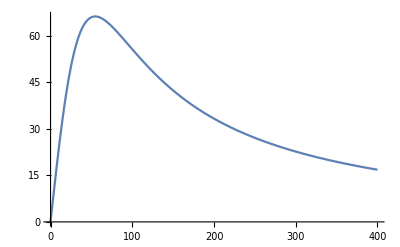

```mathematica
Plot[J[ω],{ω,0,400}]
```

```mathematica
(*S1:= -4 NIntegrate[J[ω]/ω^2 Coth[ω/(2 kB Temp)], {ω, 0, 10wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->30 ]*)
S[t_]:=-4 NIntegrate[J[ω]/ω^2 Coth[(ω β)/2] (1-Cos[ω t]), {ω, 0, 100wc}, Method -> {Automatic, "SymbolicProcessing"-> None},MaxRecursion->40 ]
```

```mathematica
rho10[t_] := ρ10i Exp[S[t]] Exp[ⅈ ϵ t]
 rho01[t_] := ρ01i Exp[S[t]] Exp[-ⅈ ϵ t]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

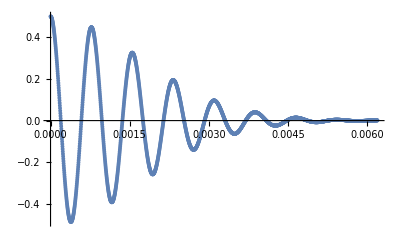

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

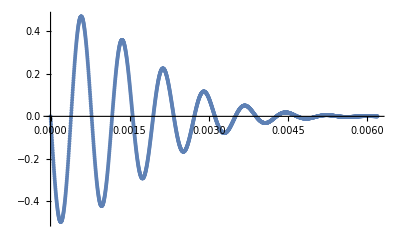

```mathematica
t0 = 0; tf= 50/ϵ; di =(tf-t0)/2000;
tlist = N[Range[t0,tf, di]];
ListPlot[Transpose@{tlist, Re@rho01[tlist]}, PlotRange->All]
ListPlot[Transpose@{tlist, Im@rho01[tlist]}, PlotRange->All]
```